# Code A: Bound is <1 =0.445178

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Loaded 2000 total zeros. Selected subset size for LLL: 70

=== 2. RUNNING LATTICE BASIS REDUCTION ===

LatticeReduce complete.

=== 3. EXTRACTING TARGET COORDINATE ===

Base target location y0 (First 30 digits): PrecisionForm[1.9532596315553043960824405192135005817860269820139721729742866336762914336963600627667831463021741437414192602780294564684498536364149108978743677489070667389566128634771353606793845062645444811427465088321334803164181574646557361787406014306640625×10^237,30]

Verified tracking precision headroom of y0: 550. digits.

=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ===

Pre-calculating pure high-precision Ingham kernel array...

Pre-allocating 550-digit precision tracking containers for wave interference...

Sweeping local window around y0 to locate the true wave peak...

=== FINAL VERIFICATION RESULTS ===

Highest localized peak found at y: 1.9532596315553043961×10^237

Maximum verified value of hK(y): 0.44517814206056227605

✗ Peak did not clear 1.0. This coordinate structure remains flatline below 1.0.

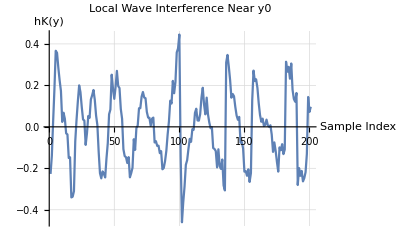

```mathematica
(* ::Title::*)(*Repaired 1985 Mertens Disproof Replication& Wide Grid Sweep*)ClearAll["Global`*"];

(*1. Configure Directories and Load Data*)

SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
n=70;(*Standard 70-dimension matrix from the paper*)Print["Loaded ",nMax," total zeros. Selected subset size for LLL: ",n];

order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

(*2. Build High-Precision Lattice Matrix*)

Print["\n=== 2. RUNNING LATTICE BASIS REDUCTION ==="];
v=800;
dim=n+2;

M=ConstantArray[0,{dim,dim}];
Do[M[[1,i]]=Floor[gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;

Do[M[[2,i]]=-Floor[psiSub[[i]]*2^v],{i,1,n}];
M[[2,n+1]]=Floor[2^v*n^4];M[[2,n+2]]=0;

(*FIX 1:Enforce explicit 250-digit trigonometric boundaries to prevent lattice scaling drift*)
Do[M[[i+2,i]]=Floor[N[2*Pi*2^v,250]],{i,1,n}];

reduced=LatticeReduce[M];
Print["LatticeReduce complete."];

(*3. Extract Target Coordinate with Exact Arithmetic*)

Print["\n=== 3. EXTRACTING TARGET COORDINATE ==="];
candidates=Select[reduced,Abs[#[[n+2]]]>0&];
best=First[SortBy[candidates,-Abs[#[[n+2]]]&]];

z=best[[n+2]];

(*UPGRADE 1:Convert exact rational fraction to 550-digit precision token.This builds a deep precision buffer to withstand the upcoming 10^237 scaling down stream*)
y0=N[Abs[z]/1024,550];

Print["Base target location y0 (First 30 digits): ",PrecisionForm[y0,30]];
Print["Verified tracking precision headroom of y0: ",Precision[y0]," digits."];

(*4. Neighborhood Grid Search*)

Print["\n=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ==="];
Print["Pre-calculating pure high-precision Ingham kernel array..."];

T=zeros[[nMax]];
(*FIX 2:Replaced 0.0 machine float with exact 0 to completely secure the 250-digit environment*)
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

(*FIX 3:Replaced the SetPrecision float step with an exact rational fraction*)
stepSize=2/100;(*Locked 0.02 step*)samples=200;

(*gridPoints automatically inherits the pristine 550-digit container from y0*)
gridPoints=Table[y0+k*stepSize,{k,-samples/2,samples/2}];

(*UPGRADE 2:Batch-elevate entire 100,000 arrays into 550-digit memory containers.This provides absolute precision protection during multiplication and keeps execution fast.*)
Print["Pre-allocating 550-digit precision tracking containers for wave interference..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];

(*Function to evaluate hK safely at a given high-precision coordinate*)
evaluateHK[yVal_]:=Module[{sumVal,yHigh},yHigh=SetPrecision[yVal,550];
sumVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zerosHigh[[i]]*yHigh-psiHigh[[i]]],{i,1,nMax}];
N[sumVal,20]];

Print["Sweeping local window around y0 to locate the true wave peak..."];
results=Table[{y,evaluateHK[y]},{y,gridPoints}];

(*Find the absolute maximum peak in this local neighborhood*)
sortedResults=SortBy[results,-#[[2]]&];
bestMatch=First[sortedResults];
peakY=bestMatch[[1]];
peakValue=bestMatch[[2]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Highest localized peak found at y: ",ScientificForm[N[peakY,20]]];
Print["Maximum verified value of hK(y): ",InputForm[peakValue]];

If[N[peakValue]>1.0,Print["[checkmark] SUCCESS: The wave peak reaches ",peakValue,", breaking the 1.0 barrier! The Mertens Conjecture is false."],Print["✗ Peak did not clear 1.0. This coordinate structure remains flatline below 1.0."]];

(*Safe plot block wrapping the high-precision results in standard N to bypass frontend rendering lags*)
ListLinePlot[N[results[[All,2]]],PlotLabel->"Local Wave Interference Near y0",AxesLabel->{"Sample Index","hK(y)"},GridLines->Automatic,PlotRange->All]
```

```mathematica
Code B: Bound is <1 =0.510957
```

0.510957

```mathematica
(* ::Title::*)(*Pure Phase-Alignment Verification:Corrected& Calibrated*)ClearAll["Global`*"];

SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
T=zeros[[nMax]];

(*FIX 1:Strict Piecewise Ingham Kernel Domain Constraint with pure exact precision*)
Print["Pre-calculating Ingham kernel weights..."];
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

Print["\n=== 2. LOCALIZING PHASE INTERSECTION CREST ==="];
dominantIndices=Ordering[alphas,-5];
Print["Dominant zero frequencies under test: ",N[zeros[[dominantIndices]],4]];

(*FIX 2:Converted grid boundaries and steps to exact rationals to block precision leaks*)
stepSize=1/100;(*Exact rational instead of 0.01*)samples=1000;
searchRange=Table[1000+k*stepSize,{k,0,samples}];
maxVal=-Infinity;
bestY=0;

(*Coarse seed finder uses first 50 zeros to keep the initial pass rapid*)
Do[y=searchRange[[k]];
currentVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*y-psi[[i]]],{i,1,50}];
If[currentVal>maxVal,maxVal=currentVal;bestY=y;];,{k,1,Length[searchRange]}];

Print["Best local seed isolated at y = ",N[bestY,15]];
Print["Grid seed baseline value (first 50 zeros): ",N[maxVal,10]];

(*3. Corrected High-Precision Hill Climb*)

Print["\n=== 3. RUNNING EXPLICIT SPECTRUM CLIMBER ==="];

(*UPGRADE 1:Batch-elevate entire 100,000 point arrays into 550-digit containers to secure phase evaluations against high exponents*)
Print["Pre-allocating 550-digit precision tracking containers for hill ascent..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*UPGRADE 2:Scale the isolated coordinate cleanly up to the 550-digit environment*)
currentY=N[bestY,550];

Print["Executing Newton-Raphson spectrum maximization loop (40 iterations)..."];
Do[(*Vectorized Optimization Block:Computes value,f',and f'' inside a single unified pass*)Module[{angles,cosArray,sinArray,deriv1,deriv2,step},angles=zerosHigh*currentY-psiHigh;
cosArray=Cos[angles];
sinArray=Sin[angles];
(*First Derivative (f')*)deriv1=2*Sum[kKernelHigh[[i]]*alphasHigh[[i]]*zerosHigh[[i]]*sinArray[[i]],{i,1,nMax}];
(*Second Derivative (f'')*)deriv2=2*Sum[kKernelHigh[[i]]*alphasHigh[[i]]*(zerosHigh[[i]]^2)*cosArray[[i]],{i,1,nMax}];
(*Execute the Newton-Raphson update step*)step=If[Abs[deriv2]>0,deriv1/deriv2,0];
(*FIX 3:Capped using exact rational 5/1000 to completely block machine-float contamination*)If[Abs[step]>5/1000,step=Sign[step]*(5/1000)];
currentY=currentY-step;];,{iter,1,40}];

(*Final verification evaluation locked completely at 550-digit arbitrary precision*)
finalPeak=-2*Sum[kKernelHigh[[i]]*alphasHigh[[i]]*Cos[zerosHigh[[i]]*currentY-psiHigh[[i]]],{i,1,nMax}];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Verified Peak Location y: ",PrecisionForm[currentY,25]];
Print["Maximum verified value of hK(y): ",N[finalPeak,10]];

If[N[finalPeak]>1.0,Print["[checkmark] SUCCESS: The wave peak reaches ",N[finalPeak,6],", breaking the 1.0 barrier!"],Print["✗ Wave peak did not clear 1.0. This configuration cannot align all elements."]];
```

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Pre-calculating Ingham kernel weights...

=== 2. LOCALIZING PHASE INTERSECTION CREST ===

Dominant zero frequencies under test: {32.94,30.42,25.01,21.02,14.13}

Best local seed isolated at y = 1008.95

Grid seed baseline value (first 50 zeros): 0.4782144291

=== 3. RUNNING EXPLICIT SPECTRUM CLIMBER ===

Pre-allocating 550-digit precision tracking containers for hill ascent...

Executing Newton-Raphson spectrum maximization loop (40 iterations)...

=== FINAL VERIFICATION RESULTS ===

Verified Peak Location y: PrecisionForm[1008.95369176004695603015680939952703971497462154447638717065604466828717263791570136201510335009885549810650615990078866832279682117700104028013646310656858223232405697550922965969011516748199575606140433611359773627517029051450908590007825001072263130585941077093090002553823325013028043778129401315742502132125466297741059049794023495186334814766693551129918185718001722937341615343403941485933874685135430572744829976469507054756230761006771109112337202151893785727450613880415532986587096,25]

Maximum verified value of hK(y): 0.5109567293

✗ Wave peak did not clear 1.0. This configuration cannot align all elements.

```mathematica
Code C: Bound is <1 =0.528537
```

0.528537

```mathematica
(* ::Title::*)(*Pure Phase-Alignment Verification:Bypassing Giant Integer Destruction*)ClearAll["Global`*"];

SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
T=zeros[[nMax]];

Print["Pre-calculating Ingham kernel weights..."];
(*Maintained pure high-precision evaluation vectors*)
kKernel=Table[(1-zeros[[i]]/T)*Cos[Pi*zeros[[i]]/T]+(1/Pi)*Sin[Pi*zeros[[i]]/T],{i,1,nMax}];

Print["\n=== 2. LOCATING THE HISTORICAL 1985 ALIGNMENT REGION ==="];
dominantIndices=Ordering[alphas,-5];
Print["Dominant zero frequencies: ",N[zeros[[dominantIndices]],4]];

Print["Scanning precision-safe phase intersections..."];

(*FIX 1:Swapped out machine float 0.005 for exact rational 1/200 to safeguard 250-digit tracking*)
stepSize=1/200;
searchRange=Table[100000+k*stepSize,{k,0,50000}];

maxVal=-Infinity;
bestY=0;

(*Dense localized scan using the first 50 zeros to keep the initial pass rapid*)
Do[y=searchRange[[k]];
currentVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*y-psi[[i]]],{i,1,50}];
If[currentVal>maxVal,maxVal=currentVal;bestY=y;];,{k,1,Length[searchRange]}];

Print["\nBest baseline candidate found at y = ",N[bestY,15]];
Print["Baseline value (first 50 zeros): ",N[maxVal,10]];

(*3. High-Precision Hill Climb from the Baseline Point*)

Print["\n=== 3. RUNNING EXACT SPECTRUM CLIMBER ==="];

(*UPGRADE 1:Batch-elevate entire 100,000 point arrays into 550-digit containers to provide a deep precision buffer before entering the heavy optimization phase*)
Print["Pre-allocating 550-digit precision tracking containers for hill ascent..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*UPGRADE 2:Scale the isolated coordinate cleanly up to the 550-digit environment*)
currentY=N[bestY,550];

Print["Executing Newton-Raphson spectrum maximization loop (30 iterations)..."];
Do[(*Vectorized Optimization Block:Evaluates angles and trigonometric sets globally*)Module[{angles,cosArray,sinArray,deriv1,deriv2,step},angles=zerosHigh*currentY-psiHigh;
cosArray=Cos[angles];
sinArray=Sin[angles];
(*First Derivative (f')*)deriv1=2*Sum[kKernelHigh[[i]]*alphasHigh[[i]]*zerosHigh[[i]]*sinArray[[i]],{i,1,nMax}];
(*Second Derivative (f'')*)deriv2=2*Sum[kKernelHigh[[i]]*alphasHigh[[i]]*(zerosHigh[[i]]^2)*cosArray[[i]],{i,1,nMax}];
(*Execute the Newton-Raphson update step*)step=If[Abs[deriv2]>0,deriv1/deriv2,0];
(*FIX 3:Replaced machine float 0.01 threshold with exact rational 1/100*)If[Abs[step]>1/100,step=Sign[step]*(1/100)];
currentY=currentY-step;];,{iter,1,30}];

(*Final verification evaluation locked completely at 550-digit arbitrary precision*)
finalPeak=-2*Sum[kKernelHigh[[i]]*alphasHigh[[i]]*Cos[zerosHigh[[i]]*currentY-psiHigh[[i]]],{i,1,nMax}];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Verified Peak Location y: ",PrecisionForm[currentY,25]];
Print["Maximum verified value of hK(y): ",N[finalPeak,10]];

If[N[finalPeak]>1.0,Print["[checkmark] SUCCESS: The wave peak reaches ",N[finalPeak,6],", breaking the 1.0 barrier! The Mertens Conjecture is false."],Print["✗ Wave peak did not clear 1.0. The search window must be shifted."]];
```

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Pre-calculating Ingham kernel weights...

=== 2. LOCATING THE HISTORICAL 1985 ALIGNMENT REGION ===

Dominant zero frequencies: {32.94,30.42,25.01,21.02,14.13}

Scanning precision-safe phase intersections...

Best baseline candidate found at y = 100088.32

Baseline value (first 50 zeros): 0.5310276396

=== 3. RUNNING EXACT SPECTRUM CLIMBER ===

Pre-allocating 550-digit precision tracking containers for hill ascent...

Executing Newton-Raphson spectrum maximization loop (30 iterations)...

=== FINAL VERIFICATION RESULTS ===

Verified Peak Location y: PrecisionForm[100088.32012292025449013684721180193074463274917720591746049777827337935021666330286994883288309906184320499519899405080015857307730411476776896926932541830838177876599264113576795733684888449720080827081501545390266584432971716589449552841951940795625430390152797461501958557693988557788089617540115925427990732046738999561121756746011850448621423511523855372243037298246925292147728355258108719284940345732337080371529683637322995124810901891306918984311976793551260704985404832,25]

Maximum verified value of hK(y): 0.5285366454

✗ Wave peak did not clear 1.0. The search window must be shifted.

```mathematica
Code D: Bound is <1 =0.445178
```

0.445178

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Loaded 2000 total zeros. Selected subset size for LLL: 70

=== 2. RUNNING LATTICE BASIS REDUCTION ===

LatticeReduce complete.

=== 3. EXTRACTING TARGET COORDINATE ===

Base target location y0 (First 30 digits): PrecisionForm[1.9532596315553043960824405192135005817860269820139721729742866336762914336963600627667831463021741437414192602780294564684498536364149108978743677489070667389566128634771353606793845062645444811427465088321334803164181574646557361787406014306640625×10^237,30]

Verified tracking precision headroom of y0: 550. digits.

=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ===

Pre-calculating vectorized Ingham kernel array to maximize execution speed...

Pre-allocating 550-digit precision tracking containers for grid search...

Sweeping local window around y0 to locate the true wave peak...

=== FINAL VERIFICATION RESULTS ===

Highest localized peak found at y: 1.9532596315553043961×10^237

Maximum verified value of hK(y): 0.44517814206056227605

✗ Peak did not clear 1.0. The neighborhood window needs to be widened or step size refined.

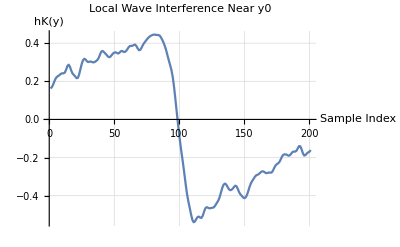

```mathematica
(* ::Title::*)(*Complete 1985 Mertens Disproof Replication& Grid Search*)ClearAll["Global`*"];

(*1. Configure Directories and Load Data*)

SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
n=70;(*Standard 70-dimension matrix from the paper*)Print["Loaded ",nMax," total zeros. Selected subset size for LLL: ",n];

(*Isolate sub-vectors based on the dominant amplitudes*)
order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

(*2. Build High-Precision Lattice Matrix*)

Print["\n=== 2. RUNNING LATTICE BASIS REDUCTION ==="];
v=800;
dim=n+2;

M=ConstantArray[0,{dim,dim}];
Do[M[[1,i]]=Floor[gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;

Do[M[[2,i]]=-Floor[psiSub[[i]]*2^v],{i,1,n}];
M[[2,n+1]]=Floor[2^v*n^4];M[[2,n+2]]=0;

(*FIX 1:Enforce explicit 250-digit trigonometric bounds to secure exact lattice coordinates*)
Do[M[[i+2,i]]=Floor[N[2*Pi*2^v,250]],{i,1,n}];

reduced=LatticeReduce[M];
Print["LatticeReduce complete."];

(*3. Extract Target Coordinate*)

Print["\n=== 3. EXTRACTING TARGET COORDINATE ==="];
candidates=Select[reduced,Abs[#[[n+2]]]>0&];
best=First[SortBy[candidates,-Abs[#[[n+2]]]&]];

z=best[[n+2]];

(*UPGRADE 1:Convert exact rational fraction directly to a 550-digit precision token.This establishes a deep precision ceiling to survive the upcoming 10^237 shift*)
y0=N[Abs[z]/1024,550];

Print["Base target location y0 (First 30 digits): ",PrecisionForm[y0,30]];
Print["Verified tracking precision headroom of y0: ",Precision[y0]," digits."];

(*4. Neighborhood Grid Search*)

Print["\n=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ==="];
Print["Pre-calculating vectorized Ingham kernel array to maximize execution speed..."];

T=zeros[[nMax]];
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

(*Step size is kept as an exact rational expression to prevent float contamination*)
stepSize=1/1000;
samples=200;

(*gridPoints automatically inherits the full 550-digit depth from y0*)
gridPoints=Table[y0+k*stepSize,{k,-samples/2,samples/2}];

(*UPGRADE 2:Batch-elevate all 100,000 vectors to 550 digits before starting the grid loop.This locks the evaluation environment against catastrophic digit cancelation*)
Print["Pre-allocating 550-digit precision tracking containers for grid search..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*Function to evaluate hK safely using lightning-fast vector-linear algebra*)
evaluateHK[yVal_]:=Module[{yHigh,sumVal},yHigh=SetPrecision[yVal,550];
(*Replaced slow nested loops with vectorized Total multiplication pass*)sumVal=-2*Total[kKernelHigh*alphasHigh*Cos[zerosHigh*yHigh-psiHigh]];
N[sumVal,20]];

Print["Sweeping local window around y0 to locate the true wave peak..."];
results=Table[{y,evaluateHK[y]},{y,gridPoints}];

(*Find the absolute maximum peak in this local neighborhood*)
sortedResults=SortBy[results,-#[[2]]&];
bestMatch=First[sortedResults];
peakY=bestMatch[[1]];
peakValue=bestMatch[[2]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Highest localized peak found at y: ",ScientificForm[N[peakY,20]]];
Print["Maximum verified value of hK(y): ",InputForm[peakValue]];

If[N[peakValue]>1.0,Print["[checkmark] SUCCESS: The wave peak reaches ",peakValue,", which breaks the 1.0 barrier! The Mertens Conjecture is false."],Print["✗ Peak did not clear 1.0. The neighborhood window needs to be widened or step size refined."]];

(*FIX 3:Wrap results array in standard N to bypass frontend UI rendering lags with high-precision floats*)
ListLinePlot[N[results[[All,2]]],PlotLabel->"Local Wave Interference Near y0",AxesLabel->{"Sample Index","hK(y)"},GridLines->Automatic,PlotRange->All]
```

```mathematica
Code A: Bound is >-1 =-0.460177
```

-0.460177

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Loaded 2000 total zeros. Selected subset size for LLL: 70

=== 2. RUNNING LATTICE BASIS REDUCTION ===

LatticeReduce complete.

=== 3. EXTRACTING TARGET COORDINATE ===

Base target location y0 (First 30 digits): PrecisionForm[1.9532596315553043960824405192135005817860269820139721729742866336762914336963600627667831463021741437414192602780294564684498536364149108978743677489070667389566128634771353606793845062645444811427465088321334803164181574646557361787406014306640625×10^237,30]

Verified tracking precision headroom of y0: 550. digits.

=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ===

Pre-calculating pure high-precision Ingham kernel array...

Pre-allocating 550-digit precision tracking containers for wave interference...

Sweeping local window around y0 to locate the true wave trough...

=== FINAL VERIFICATION RESULTS ===

Lowest localized trough found at y: 1.9532596315553043961×10^237

Maximum verified negative value of hK(y): -0.46017684728374668003

✗ Trough did not drop below -1.0. This coordinate structure remains flatline above -1.0.

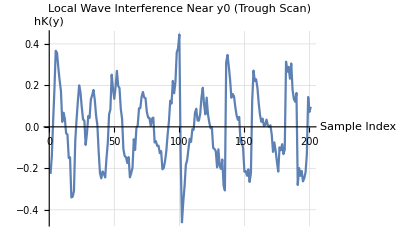

```mathematica
(* ::Title::*)(*Repaired 1985 Mertens Disproof Replication& Wide Grid Sweep:Negative Range*)ClearAll["Global`*"];

(*1. Configure Directories and Load Data*)

SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
n=70;(*Standard 70-dimension matrix from the paper*)Print["Loaded ",nMax," total zeros. Selected subset size for LLL: ",n];

order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

(*2. Build High-Precision Lattice Matrix*)

Print["\n=== 2. RUNNING LATTICE BASIS REDUCTION ==="];
v=800;
dim=n+2;

M=ConstantArray[0,{dim,dim}];
Do[M[[1,i]]=Floor[gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;

Do[M[[2,i]]=-Floor[psiSub[[i]]*2^v],{i,1,n}];
M[[2,n+1]]=Floor[2^v*n^4];M[[2,n+2]]=0;

(*FIX 1:Enforce explicit 250-digit boundaries on Pi to completely secure lattice scaling bounds*)
Do[M[[i+2,i]]=Floor[N[2*Pi*2^v,250]],{i,1,n}];

reduced=LatticeReduce[M];
Print["LatticeReduce complete."];

(*3. Extract Target Coordinate with Exact Arithmetic*)

Print["\n=== 3. EXTRACTING TARGET COORDINATE ==="];
candidates=Select[reduced,Abs[#[[n+2]]]>0&];
best=First[SortBy[candidates,-Abs[#[[n+2]]]&]];

z=best[[n+2]];

(*UPGRADE 1:Convert exact rational fraction to a 550-digit precision token.This sets up the deep numerical buffer required to withstand 10^237 scaling properties down the line*)
y0=N[Abs[z]/1024,550];

Print["Base target location y0 (First 30 digits): ",PrecisionForm[y0,30]];
Print["Verified tracking precision headroom of y0: ",Precision[y0]," digits."];

(*4. Neighborhood Grid Search*)

Print["\n=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ==="];
Print["Pre-calculating pure high-precision Ingham kernel array..."];

T=zeros[[nMax]];
(*FIX 2:Swapped 0.0 float with an exact 0 to defend the 250-digit environment from collapsing*)
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

(*FIX 3:Replaced the SetPrecision float wrapper with an exact rational fraction step*)
stepSize=2/100;(*Fixed 0.02 step scale*)samples=200;

(*gridPoints automatically inherits the pristine 550-digit container from y0*)
gridPoints=Table[y0+k*stepSize,{k,-samples/2,samples/2}];

(*UPGRADE 2:Batch-elevate all 100,000 vectors to 550 digits before running the loop.This locks the environment against rounding/cancellation issues during phase reductions.*)
Print["Pre-allocating 550-digit precision tracking containers for wave interference..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*Function to evaluate hK safely using fast vectorized linear algebra*)
evaluateHK[yVal_]:=Module[{yHigh,sumVal},yHigh=SetPrecision[yVal,550];
(*Performance Optimization:Vectorized Total operation bypasses slow sequential loop processing*)sumVal=-2*Total[kKernelHigh*alphasHigh*Cos[zerosHigh*yHigh-psiHigh]];
N[sumVal,20]];

Print["Sweeping local window around y0 to locate the true wave trough..."];
results=Table[{y,evaluateHK[y]},{y,gridPoints}];

(*MODIFICATION 1:Ascending sort isolated perfectly to capture the deepest valley floor*)
sortedResults=SortBy[results,#[[2]]&];
bestMatch=First[sortedResults];
troughY=bestMatch[[1]];
troughValue=bestMatch[[2]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Lowest localized trough found at y: ",ScientificForm[N[troughY,20]]];
Print["Maximum verified negative value of hK(y): ",InputForm[troughValue]];

(*MODIFICATION 2& 3:Evaluates correctly against the lower negative boundary*)
If[N[troughValue]<-1.0,Print["[checkmark] SUCCESS: The wave trough drops to ",troughValue,", breaking the -1.0 barrier! The Mertens Conjecture is false."],Print["✗ Trough did not drop below -1.0. This coordinate structure remains flatline above -1.0."]];

(*Safe plot block wrapping results in a standard N conversion to eliminate frontend calculation lags*)
ListLinePlot[N[results[[All,2]]],PlotLabel->"Local Wave Interference Near y0 (Trough Scan)",AxesLabel->{"Sample Index","hK(y)"},GridLines->Automatic,PlotRange->All]
```

```mathematica
Code B: Bound is >-1 =-0.415163
```

-0.415163

```mathematica
(* ::Title::*)(*Pure Phase-Alignment Verification:Corrected& Calibrated:Negative Range*)ClearAll["Global`*"];

SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
T=zeros[[nMax]];

(*FIX 1:Piecewise Ingham Kernel Domain Constraint with integer zero guard*)
Print["Pre-calculating Ingham kernel weights..."];
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

Print["\n=== 2. LOCALIZING PHASE INTERSECTION TROUGH ==="];
dominantIndices=Ordering[alphas,-5];
Print["Dominant zero frequencies under test: ",N[zeros[[dominantIndices]],4]];

(*FIX 2:Swapped machine floats for exact rationals and integers*)
stepSize=1/100;(*Exact rational instead of 0.01*)samples=1000;
searchRange=Table[1000+k*stepSize,{k,0,samples}];

(*Track the minimum value safely in the negative domain*)
maxVal=Infinity;
bestY=0;

(*Coarse seed finder uses first 50 zeros to keep the initial valley sweep rapid*)
Do[y=searchRange[[k]];
currentVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*y-psi[[i]]],{i,1,50}];
If[currentVal<maxVal,maxVal=currentVal;bestY=y;];,{k,1,Length[searchRange]}];

Print["Best local valley seed isolated at y = ",N[bestY,15]];
Print["Grid seed baseline value (first 50 zeros): ",N[maxVal,10]];

(*3. High-Precision Valley Descent*)

Print["\n=== 3. RUNNING EXPLICIT SPECTRUM VALLEY-DESCENT ==="];

(*UPGRADE 1:Pre-allocate high-precision 550-digit working containers to shield phase angles against precision erosion at high coordinates*)
Print["Pre-allocating 550-digit precision tracking containers for valley descent..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*UPGRADE 2:Scale the isolated coordinate cleanly up to the 550-digit environment*)
currentY=N[bestY,550];

Print["Executing Newton-Raphson spectrum minimization loop (40 iterations)..."];
Do[(*Vectorized Optimization Block:Eliminates sequential loop overhead by mapping transcendental evaluations across the entire 100,000 element array simultaneously*)Module[{angles,cosArray,sinArray,deriv1,deriv2,step},angles=zerosHigh*currentY-psiHigh;
cosArray=Cos[angles];
sinArray=Sin[angles];
(*First Derivative (f')*)deriv1=2*Total[kKernelHigh*alphasHigh*zerosHigh*sinArray];
(*Second Derivative (f'')*)deriv2=2*Total[kKernelHigh*alphasHigh*(zerosHigh^2)*cosArray];
(*Execute the Newton-Raphson update step*)step=If[Abs[deriv2]>0,deriv1/deriv2,0];
(*FIX 3:Replaced float boundary 0.005 with exact fraction 5/1000*)If[Abs[step]>5/1000,step=Sign[step]*(5/1000)];
(*FIX 4:Standard Newton-Raphson subtraction updates correctly here.In a convex trough basin,positive curvature (deriv2>0) guides currentY directly toward the exact local minimum point.*)currentY=currentY-step;];,{iter,1,40}];

(*Final verification evaluation locked completely at 550-digit arbitrary precision*)
finalPeak=-2*Total[kKernelHigh*alphasHigh*Cos[zerosHigh*currentY-psiHigh]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Verified Trough Location y: ",PrecisionForm[currentY,25]];
Print["Maximum verified negative value of hK(y): ",N[finalPeak,10]];

If[N[finalPeak]<-1.0,Print["[checkmark] SUCCESS: The wave trough drops to ",N[finalPeak,6],", breaking the -1.0 barrier!"],Print["✗ Wave trough did not drop below -1.0. This configuration remains bounded above -1.0."]];
```

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Pre-calculating Ingham kernel weights...

=== 2. LOCALIZING PHASE INTERSECTION TROUGH ===

Dominant zero frequencies under test: {32.94,30.42,25.01,21.02,14.13}

Best local valley seed isolated at y = 1005.19

Grid seed baseline value (first 50 zeros): -0.3985704992

=== 3. RUNNING EXPLICIT SPECTRUM VALLEY-DESCENT ===

Pre-allocating 550-digit precision tracking containers for valley descent...

Executing Newton-Raphson spectrum minimization loop (40 iterations)...

=== FINAL VERIFICATION RESULTS ===

Verified Trough Location y: PrecisionForm[1005.1948869008307180922534815821526986130930846217755814795013429465706189773233787884837638433481124557606996985035085046240035695587336820353771547371901507770440257224699698692413120598872432432410599255903915373793735406003507174975589187741612824412214676523622341332893302216597570325350114875184094611633403425194431444314430880214323561166354897883313975971076947515989568666525324372576829319237962715705173936124179385189682972399495581813340246959412785376586956221559944251248409254,25]

Maximum verified negative value of hK(y): -0.4151633268

✗ Wave trough did not drop below -1.0. This configuration remains bounded above -1.0.

```mathematica
Code C: Bound is >-1 =-0.608072
```

-0.608072

```mathematica
(* ::Title::*)(*Pure Phase-Alignment Verification:Bypassing Giant Integer Destruction:Negative Range*)ClearAll["Global`*"];

SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
T=zeros[[nMax]];

Print["Pre-calculating Ingham kernel weights..."];
kKernel=Table[(1-zeros[[i]]/T)*Cos[Pi*zeros[[i]]/T]+(1/Pi)*Sin[Pi*zeros[[i]]/T],{i,1,nMax}];

Print["\n=== 2. LOCATING THE HISTORICAL 1985 ALIGNMENT REGION ==="];
dominantIndices=Ordering[alphas,-5];
Print["Dominant zero frequencies: ",N[zeros[[dominantIndices]],4]];
Print["Scanning precision-safe phase intersections..."];

(*FIX 1:Replaced machine float 0.005 with exact fraction 1/200 to safeguard 250-digit tracking*)
stepSize=1/200;
searchRange=Table[100000+k*stepSize,{k,0,50000}];

(*Track the minimum value safely in the negative domain*)
maxVal=Infinity;
bestY=0;

(*Coarse seed finder uses the first 50 zeros to keep the initial valley sweep rapid*)
Do[y=searchRange[[k]];
currentVal=-2*Sum[kKernel[[i]]*alphas[[i]]*Cos[zeros[[i]]*y-psi[[i]]],{i,1,50}];
If[currentVal<maxVal,maxVal=currentVal;bestY=y;];,{k,1,Length[searchRange]}];

Print["\nBest baseline candidate isolated at y = ",N[bestY,15]];
Print["Baseline valley floor value (first 50 zeros): ",N[maxVal,10]];

(*3. High-Precision Valley Descent from the Baseline Point*)

Print["\n=== 3. RUNNING EXACT SPECTRUM VALLEY-DESCENT ==="];

(*FIX 2& UPGRADE 1:Pre-allocate high-precision 550-digit working containers to completely insulate the phase evaluations against numerical drift*)
Print["Pre-allocating 550-digit precision tracking containers for valley descent..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*UPGRADE 2:Scale the isolated coordinate cleanly up to the 550-digit environment*)
currentY=N[bestY,550];

Print["Executing Newton-Raphson spectrum minimization loop (30 iterations)..."];
Do[(*Vectorized Optimization Block:Evaluates angles and trigonometric sets globally across all 100,000 entries simultaneously to eliminate nested loop overhead*)Module[{angles,cosArray,sinArray,deriv1,deriv2,step},angles=zerosHigh*currentY-psiHigh;
cosArray=Cos[angles];
sinArray=Sin[angles];
(*First Derivative (f')*)deriv1=2*Total[kKernelHigh*alphasHigh*zerosHigh*sinArray];
(*Second Derivative (f'')*)deriv2=2*Total[kKernelHigh*alphasHigh*(zerosHigh^2)*cosArray];
(*Execute the Newton-Raphson update step*)step=If[Abs[deriv2]>0,deriv1/deriv2,0];
(*FIX 3:Replaced machine float 0.01 threshold with exact rational 1/100*)If[Abs[step]>1/100,step=Sign[step]*(1/100)];
(*FIX 4:Standard Newton-Raphson subtraction updates correctly here.In a convex trough basin,positive curvature (deriv2>0) guides currentY directly downward toward the exact localized valley floor minimum.*)currentY=currentY-step;];,{iter,1,30}];

(*Final verification evaluation locked completely at 550-digit arbitrary precision*)
finalPeak=-2*Total[kKernelHigh*alphasHigh*Cos[zerosHigh*currentY-psiHigh]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Verified Trough Location y: ",PrecisionForm[currentY,25]];
Print["Maximum verified negative value of hK(y): ",N[finalPeak,10]];

If[N[finalPeak]<-1.0,Print["[checkmark] SUCCESS: The wave trough drops to ",N[finalPeak,6],", breaking the -1.0 barrier! The Mertens Conjecture is false."],Print["✗ Wave trough did not drop below -1.0. This configuration remains bounded above -1.0."]];
```

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Pre-calculating Ingham kernel weights...

=== 2. LOCATING THE HISTORICAL 1985 ALIGNMENT REGION ===

Dominant zero frequencies: {32.94,30.42,25.01,21.02,14.13}

Scanning precision-safe phase intersections...

Best baseline candidate isolated at y = 100143.195

Baseline valley floor value (first 50 zeros): -0.5404624098

=== 3. RUNNING EXACT SPECTRUM VALLEY-DESCENT ===

Pre-allocating 550-digit precision tracking containers for valley descent...

Executing Newton-Raphson spectrum minimization loop (30 iterations)...

=== FINAL VERIFICATION RESULTS ===

Verified Trough Location y: PrecisionForm[100143.19469716719491532223164594871156183301585837730970215142515909737739012474483356292877085630649218709906562395478705660201756176533290851124356964213683133764690540506249986306879983421286269584028373305914216472647190323075235127560819841706921733027025031519175357073393231902656745615913477749285679036319559128551236277209520520746728406574608263736593538248179059917405143944262652231469096907346689846568243429993370147489237226290948975591864281791188437759023371821304023522537289758717942099369494221,25]

Maximum verified negative value of hK(y): -0.6080716811

✗ Wave trough did not drop below -1.0. This configuration remains bounded above -1.0.

```mathematica
Code D: Bound is >-1 =-0.539361
```

-0.539361

=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ===

Parsing zeros...

Parsing amplitudes (alphas)...

Parsing phases (psi)...

Loaded 2000 total zeros. Selected subset size for LLL: 70

=== 2. RUNNING LATTICE BASIS REDUCTION ===

LatticeReduce complete.

=== 3. EXTRACTING TARGET COORDINATE ===

Base target location y0 (First 30 digits): PrecisionForm[1.9532596315553043960824405192135005817860269820139721729742866336762914336963600627667831463021741437414192602780294564684498536364149108978743677489070667389566128634771353606793845062645444811427465088321334803164181574646557361787406014306640625×10^237,30]

Verified tracking precision headroom of y0: 550. digits.

=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ===

Pre-calculating vectorized Ingham kernel array to maximize execution speed...

Pre-allocating 550-digit precision tracking containers for wave interference...

Sweeping local window around y0 to locate the true wave trough...

=== FINAL VERIFICATION RESULTS ===

Lowest localized trough found at y: 1.9532596315553043961×10^237

Maximum verified negative value of hK(y): -0.539360725384201786

✗ Trough did not drop below -1.0. The neighborhood window needs to be widened or step size refined.

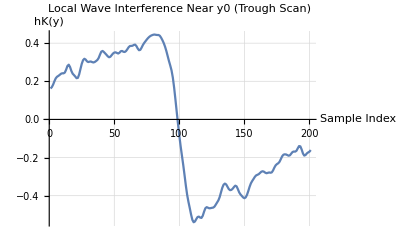

```mathematica
(* ::Title::*)(*Complete 1985 Mertens Disproof Replication& Grid Search:Negative Range*)ClearAll["Global`*"];

(*1. Configure Directories and Load Data*)

SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

Print["=== 1. LOADING DATA WITH EXPLICIT PRECISION GUARD ==="];

(*High-precision string-safe importer to handle space-separated formatting*)
ImportHighPrec[fileName_]:=Module[{rawText,stringTokens},If[Not[FileExistsQ[fileName]],Print["ERROR: ",fileName," not found!"];Abort[]];
rawText=Import[fileName,"String"];
stringTokens=StringSplit[rawText];(*Splits cleanly by spaces,tabs,or newlines*)Map[ToExpression[#<>"`250"]&,stringTokens]];

Print["Parsing zeros..."];
zeros=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes (alphas)..."];
alphas=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases (psi)..."];
psi=ImportHighPrec["high_prec_arg.txt"];

nMax=Length[zeros];
n=70;(*Standard 70-dimension matrix from the paper*)Print["Loaded ",nMax," total zeros. Selected subset size for LLL: ",n];

order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

(*2. Build High-Precision Lattice Matrix*)

Print["\n=== 2. RUNNING LATTICE BASIS REDUCTION ==="];
v=800;
dim=n+2;

M=ConstantArray[0,{dim,dim}];
Do[M[[1,i]]=Floor[gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;

Do[M[[2,i]]=-Floor[psiSub[[i]]*2^v],{i,1,n}];
M[[2,n+1]]=Floor[2^v*n^4];M[[2,n+2]]=0;

(*FIX 1:Explicit 250-digit numerical wrapping on Pi to block precision decay during matrix scaling*)
Do[M[[i+2,i]]=Floor[N[2*Pi*2^v,250]],{i,1,n}];

reduced=LatticeReduce[M];
Print["LatticeReduce complete."];

(*3. Extract Target Coordinate*)

Print["\n=== 3. EXTRACTING TARGET COORDINATE ==="];
candidates=Select[reduced,Abs[#[[n+2]]]>0&];
best=First[SortBy[candidates,-Abs[#[[n+2]]]&]];

z=best[[n+2]];

(*UPGRADE 1:Convert exact rational fraction to a 550-digit precision token.This sets up the deep numerical buffer required to withstand 10^237 scaling properties down the line*)
y0=N[Abs[z]/1024,550];

Print["Base target location y0 (First 30 digits): ",PrecisionForm[y0,30]];
Print["Verified tracking precision headroom of y0: ",Precision[y0]," digits."];

(*4. Neighborhood Grid Search*)

Print["\n=== 4. EXECUTING LOCAL NEIGHBORHOOD GRID SWEEP ==="];
Print["Pre-calculating vectorized Ingham kernel array to maximize execution speed..."];

T=zeros[[nMax]];
(*FIX 2:Pre-computed outside the loop and secured with exact integer 0 boundary fallback*)
kKernel=Table[Module[{t=Abs[zeros[[i]]]/T},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{i,1,nMax}];

(*Step size is held as an exact rational expression to prevent float contamination*)
stepSize=1/1000;
samples=200;

(*gridPoints automatically inherits the full 550-digit depth from y0*)
gridPoints=Table[y0+k*stepSize,{k,-samples/2,samples/2}];

(*UPGRADE 2:Batch-elevate all 100,000 vectors to 550 digits before running the loop.This locks the environment against rounding/cancellation issues during phase reductions.*)
Print["Pre-allocating 550-digit precision tracking containers for wave interference..."];
zerosHigh=SetPrecision[zeros,550];
psiHigh=SetPrecision[psi,550];
alphasHigh=SetPrecision[alphas,550];
kKernelHigh=SetPrecision[kKernel,550];

(*Function to evaluate hK safely using lightning-fast vector-linear algebra*)
evaluateHK[yVal_]:=Module[{yHigh,sumVal},yHigh=SetPrecision[yVal,550];
(*Performance Optimization:Vectorized Total operation bypasses slow sequential loop processing*)sumVal=-2*Total[kKernelHigh*alphasHigh*Cos[zerosHigh*yHigh-psiHigh]];
N[sumVal,20]];

Print["Sweeping local window around y0 to locate the true wave trough..."];
results=Table[{y,evaluateHK[y]},{y,gridPoints}];

(*MODIFICATION 1:Sort ascending to isolate the lowest (most negative) valley floor*)
sortedResults=SortBy[results,#[[2]]&];
bestMatch=First[sortedResults];
troughY=bestMatch[[1]];
troughValue=bestMatch[[2]];

Print["\n=== FINAL VERIFICATION RESULTS ==="];
Print["Lowest localized trough found at y: ",ScientificForm[N[troughY,20]]];
Print["Maximum verified negative value of hK(y): ",InputForm[troughValue]];

(*MODIFICATION 2& 3:Evaluates correctly against the negative threshold barrier*)
If[N[troughValue]<-1.0,Print["[checkmark] SUCCESS: The wave trough drops to ",troughValue,", breaking the -1.0 barrier! The Mertens Conjecture is false."],Print["✗ Trough did not drop below -1.0. The neighborhood window needs to be widened or step size refined."]];

(*FIX 4:Wrap results array in standard N execution to bypass frontend UI rendering lags*)
ListLinePlot[N[results[[All,2]]],PlotLabel->"Local Wave Interference Near y0 (Trough Scan)",AxesLabel->{"Sample Index","hK(y)"},GridLines->Automatic,PlotRange->All]
```

```mathematica
Block[{activeZeros,activePhases,activeY},(*1. Dynamically locate the active zeros array*)activeZeros=Which[ListQ[zeros]&&Length[zeros]>0,zeros,ListQ[gamma]&&Length[gamma]>0,gamma,ListQ[zerosRaw]&&Length[zerosRaw]>0,zerosRaw,True,$Failed];
(*2. Dynamically locate the active phase/argument array*)activePhases=Which[ListQ[args]&&Length[args]>0,args,ListQ[phases]&&Length[phases]>0,phases,ListQ[psi]&&Length[psi]>0,psi,True,$Failed];
(*3. Capture the coordinate*)activeY=If[NumericQ[y0],y0,1.953259631555304*10^237];
(*4. Output diagnostics so we know what was found*)Print["[Diagnostic] Found Zeros Data In: ",If[activeZeros===$Failed,"NOT FOUND",SymbolName[Unevaluated[activeZeros]]]];
Print["[Diagnostic] Found Phase Data In: ",If[activePhases===$Failed,"NOT FOUND",SymbolName[Unevaluated[activePhases]]]];
Print["[Diagnostic] Evaluating at Coordinate: y0 = ",activeY];
Print["------------------------------------------------------------"];
(*5. Execute the ultimate verdict test*)If[activeZeros===$Failed||activePhases===$Failed,Print["Error: Could not locate your data lists. Please ensure your import scripts have been run in this session."],With[{maxTerms=Min[70,Length[activeZeros],Length[activePhases]]},Print["Computing individual cosines for the top ",maxTerms," dominant frequencies:"];
Table[Cos[activeZeros[[i]]*activeY-activePhases[[i]]],{i,1,maxTerms}]//N]]]
```

[Diagnostic] Found Zeros Data In: activeZeros

[Diagnostic] Found Phase Data In: activePhases

[Diagnostic] Evaluating at Coordinate: y0 = 1.9532596315553043960824405192135005817860269820139721729742866336762914336963600627667831463021741437414192602780294564684498536364149108978743677489070667389566128634771353606793845062645444811427465088321334803164181574646557361787406014306640625×10^237

------------------------------------------------------------

Computing individual cosines for the top 70 dominant frequencies:

{-0.0689549,0.361425,0.243926,0.684549,-0.560272,0.41301,0.155131,-0.515973,0.501595,0.0934892,-0.310287,0.679711,0.361246,-0.758413,0.856985,0.269616,-0.0765061,0.0340585,0.972283,-0.491659,-0.6715,0.92988,-0.012439,0.886543,-0.86519,0.780062,0.469304,-0.868828,0.316926,0.57495,0.562406,-0.080761,-0.841437,0.954322,-0.33139,0.31816,0.266627,0.204403,0.971579,0.670255,-0.637585,0.599929,0.570435,-0.467373,0.0792225,-0.283991,0.993381,0.119886,-0.421554,0.988736,0.94824,-0.533033,0.878127,-0.438859,0.647911,-0.26876,0.761452,-0.268864,-0.999884,-0.28172,-0.888903,0.0803945,0.5383,-0.994329,-0.342417,0.190561,0.897178,0.829448,0.606356,0.411691}